## Weak Lensing Checks

## Test and Plot WL Quantities

```mathematica
powerSpectrum[0.01,100]
```

0.134535

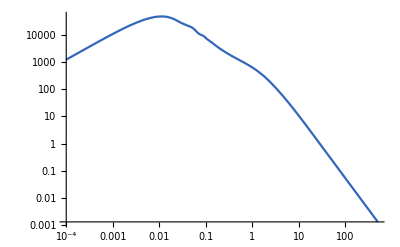

```mathematica
LogLogPlot[{powerSpectrum[0.5, kkk]}, {kkk,0.0001,500}, PlotLegends->Automatic, PlotRange->Automatic]
```

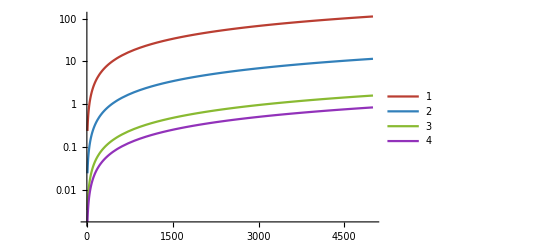

```mathematica
LogPlot[{ kofell[0.01,ell],kofell[0.1,ell], kofell[0.9,ell], kofell[2.5,ell]}, {ell,10,5000}, PlotLegends->Automatic, PlotRange->Automatic]
```

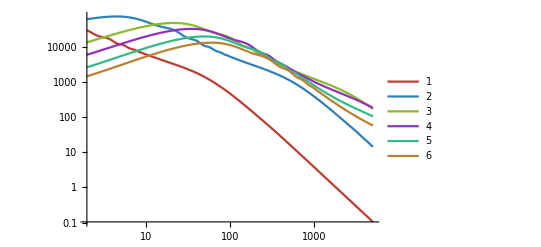

```mathematica
LogLogPlot[Evaluate@(pLimber[#, eee]&/@{0.01,0.1,0.5,0.9,1.5,2.1}), {eee,2,5000}, PlotLegends->Automatic, PlotRange->All]
```

```mathematica
$zbinsEquiPopu
```

{0.001,0.417121,0.558605,0.675825,0.785857,0.896692,1.01497,1.1494,1.31638,1.56301,2.5}

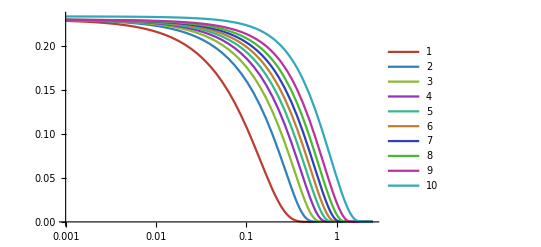

```mathematica
LogLinearPlot[{Evaluate@(lensKernelGG[zz, #,# ]&/@Range[1,10])}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotRange->All]
```

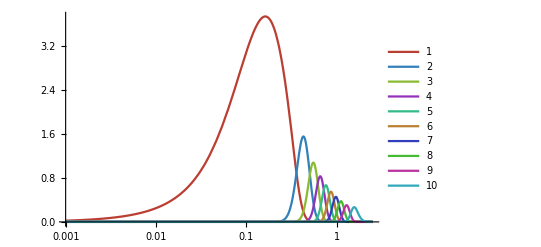

```mathematica
LogLinearPlot[{Evaluate@(lensKernelGI[zz, #,# ]&/@Range[1,10])}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotRange->All]
```

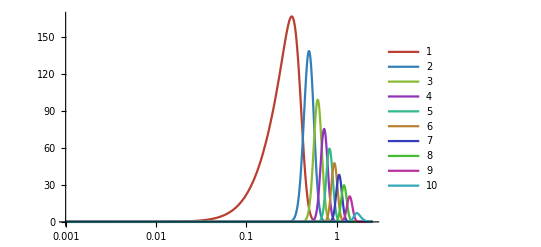

```mathematica
LogLinearPlot[{Evaluate@(lensKernelII[zz, #,# ]&/@Range[1,10])}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotRange->All]
```

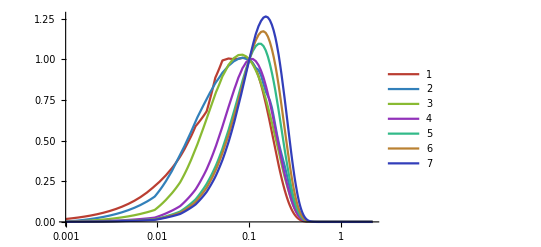

```mathematica
LogLinearPlot[Evaluate@((pijIntegrandGGInterpolFunc[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]
```

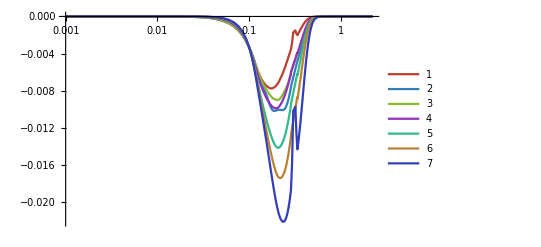

```mathematica
LogLinearPlot[Evaluate@((pijIntegrandGIInterpolFunc[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]
```

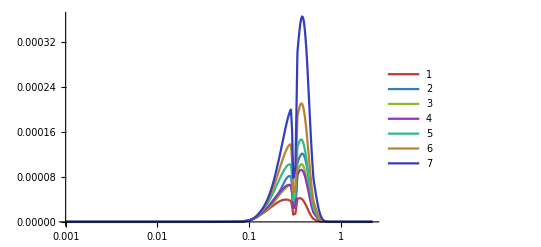

```mathematica
LogLinearPlot[Evaluate@((pijIntegrandIIInterpolFunc[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]
```

```mathematica
(*LogLinearPlot[Evaluate@((WeakLensingFisherTools`DIAInterpol[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]*)
```

```mathematica
CijGG[150,2,2, shearshearIntegrand->pijIntegrandGGInterpolFunc]//AbsoluteTiming
```

{0.221436,1.95492×10^-9}

```mathematica
CijGG[150,2,2, shearshearIntegrand->pijIntegrandGG]//AbsoluteTiming
```

{0.930506,1.95496×10^-9}

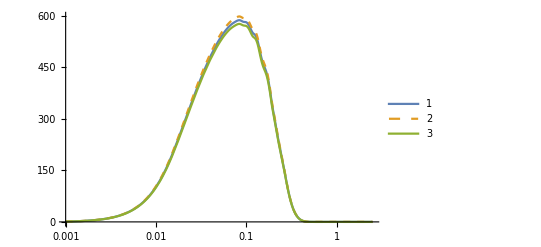

```mathematica
LogLinearPlot[{ pijIntegrandGGInterpolFunc[zz, 100, 1,1 ], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[Omegam, $epsilonstep]], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[Omegam, -$epsilonstep]]}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotStyle->{Thick, Dashed, Thick, DotDashed}]
```

```mathematica
$paramoptions
```

{Omegam→0.32,Omegab→0.05,hubble→0.67,ns→0.96,sigma8→0.911031,logfR0→-4.30103,$aIA→1.72,$eIA→-0.41,$bIA→2.17}

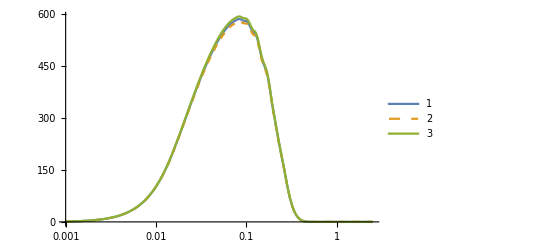

```mathematica
LogLinearPlot[{ pijIntegrandGGInterpolFunc[zz, 100, 1,1 ], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[logfR0, $epsilonstep]], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[logfR0, -$epsilonstep]]}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotStyle->{Thick, Dashed, Thick, DotDashed}]
```

```mathematica
ello=1000;
```

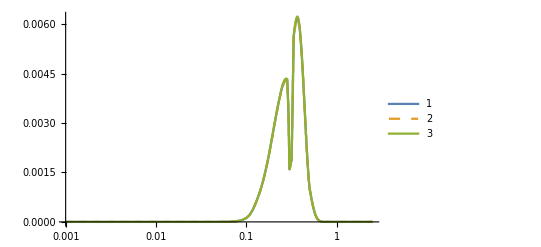

```mathematica
LogLinearPlot[{ pijIntegrandIIInterpolFunc[zz, ello, 1,1 ], pijIntegrandIIInterpolFunc[zz, ello, 1,1 , epsilonChangeParameter[logfR0, $epsilonstep]], pijIntegrandIIInterpolFunc[zz, ello, 1,1 , epsilonChangeParameter[logfR0, -$epsilonstep]]}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotStyle->{Thick, Dashed, Thick, DotDashed}, PlotRange->All]
```

```mathematica
Options[DIAInterpolTest]=$paramoptions;
DIAInterpolTest[ell_,opts:OptionsPattern[]]:=DIAInterpolTest[ell,opts]=Block[{ret,OmegaM0,zz},OmegaM0=OmegaM0Today[opts];
Interpolation[Table[{zz,((OmegaM0/Growth[zz,kofell[zz,ell,opts],opts])*curlyFIA[zz,opts])},{zz,$zminSurvey,$zmaxSurvey,($zmaxSurvey-$zminSurvey)/$zintepoints}]]];
```

```mathematica
DIAInterpolTest[1000]
```

InterpolatingFunction[…]

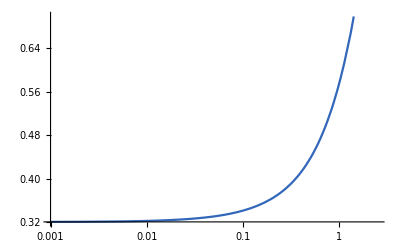

```mathematica
LogLinearPlot[0.32/Growth[zz,kofell[zz,1000]], {zz,0.001,2.5}]
```

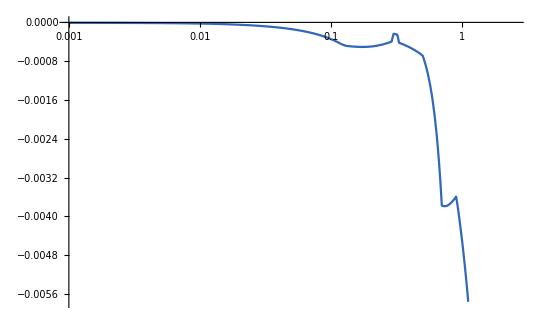

```mathematica
LogLinearPlot[curlyFIA[zz], {zz,0.001,2.5}]
```

```mathematica
cijStd=Table[{lll,CijGG[lll,2,1, shearshearIntegrand->pijIntegrandGG]}, {lll,$ellbinscenters}];
```

```mathematica
cijInt=Table[{lll,CijGG[lll,2,1, shearshearIntegrand->pijIntegrandGGInterpolFunc]}, {lll,$ellbinscenters}];
```

```mathematica
cijAllInt=Table[{lll,Cij[lll,2,1, shearshearIntegrand->pijIntegrandGGInterpolFunc]}, {lll,$ellbinscenters}];
```

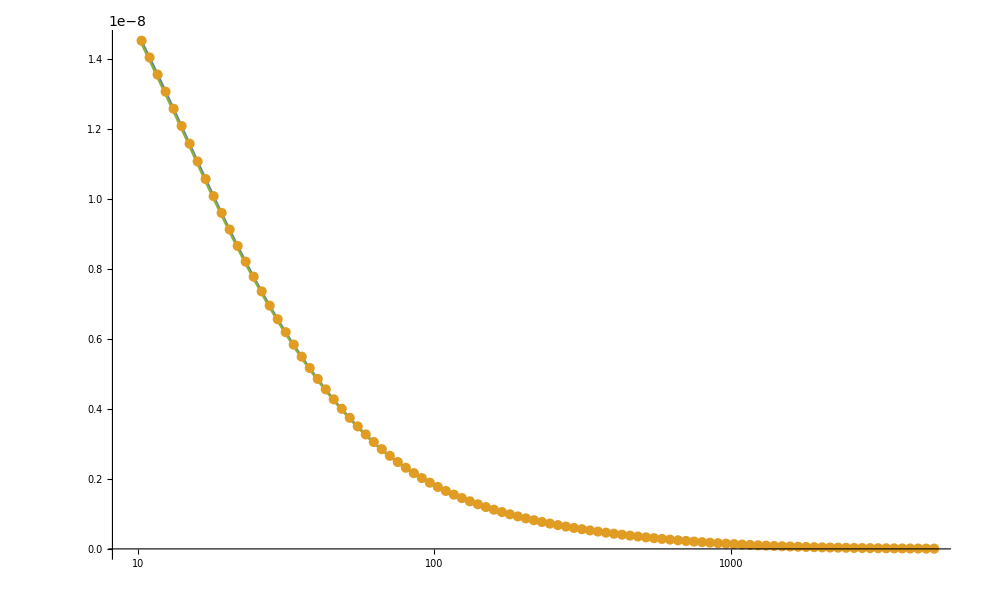

```mathematica
ListLogLinearPlot[{cijStd, cijInt, cijAllInt}, Joined->{True,False}]
```

```mathematica
Cij[100,1,1]
```

1.24021×10^-9

```mathematica
curlyFIASymbol[z_,aia_,bia_,eia_]:=(-1*aia*cia*((1+z)^eia *( lumo[z])^bia))
```

```mathematica
pijIntegrandSymbolOfZ[z_,aia_,bia_,eia_]:=((OmegaM0/Growth0[z])^2*curlyFIASymbol[z,aia,bia,eia]^2*lensII[z]*pLimb[z])
```

```mathematica
$aIAfidu
```

1.72

```mathematica
D[curlyFIASymbol[z,Aia,Bia,Eia],Aia]
```

-cia (1+z)^Eia lumo[z]^Bia

```mathematica
D[curlyFIASymbol[z,Aia,Bia,Eia],Eia]
```

-Aia cia (1+z)^Eia Log[1+z] lumo[z]^Bia

```mathematica
D[pijIntegrandSymbol[z,Aia,Bia,Eia],Eia]
```

(2 Aia^2 cia^2 lensII OmegaM0^2 pLimb (1+z)^(2 Eia) Log[1+z] lumo[z]^(2 Bia))/Growth0^2

```mathematica
$parampositions
```

{Omegam→1,Omegab→2,hubble→3,ns→4,sigma8→5,logfR0→6,$aIA→7,$eIA→8,$bIA→9}

```mathematica
alpha=9;
{opt1,opt2,step}=numericalDerivativeStep[alpha,$epsilonstep];
opt1
opt2
step
ztesta=0.2
elltesta=1000;
it=1;
jt=1;
deriv$pijII = (pijIntegrandII[ztesta, elltesta,it, jt,  opt1]-pijIntegrandII[ztesta, elltesta,it, jt, opt2])/step
```

$bIA→2.1917

$bIA→2.1483

0.0434

0.2

-0.00967911

```mathematica
symbolderiv$pijII$Aia=D[pijIntegrandSymbolOfZ[ztesta,Aia,Bia,Eia],Bia]
```

(2 1.2^(2 Eia) Aia^2 cia^2 OmegaM0^2 lensII[0.2] Log[lumo[0.2]] lumo[0.2]^(2 Bia) pLimb[0.2])/Growth0[0.2]^2

```mathematica
symbolderiv$pijII$Aia/.{Eia->$eIAfidu, Aia->$aIAfidu, Bia->$bIAfidu, OmegaM0->OmegaM0Today[], pLimb[ztesta]->pLimber[ztesta,elltesta], Growth0[ztesta]->Growth[ztesta,kofell[ztesta,elltesta]], cia->$cIA, lumo[ztesta]->$luminosityFileInterpolation[ztesta], lensII[ztesta]->lensKernelII[ztesta,it,jt]}
```

-0.00967001

```mathematica
Integrate[pijIntegrandSymbolOfZ[zz,Aia,Bia,Eia], zz]
```

Aia^2 cia^2 OmegaM0^2 ∫((1+zz)^(2 Eia) lensII[zz] lumo[zz]^(2 Bia) pLimb[zz])/Growth0[zz]^2 ⅆzz

```mathematica
D[Integrate[pijIntegrandSymbolOfZ[zz,Aia,Bia,Eia], zz], Aia]
```

2 Aia cia^2 OmegaM0^2 ∫((1+zz)^(2 Eia) lensII[zz] lumo[zz]^(2 Bia) pLimb[zz])/Growth0[zz]^2 ⅆzz

```mathematica
D[Integrate[pijIntegrandSymbolOfZ[zz,Aia,Bia,Eia], zz], Bia]
```

2 Aia^2 cia^2 OmegaM0^2 ∫((1+zz)^(2 Eia) lensII[zz] Log[lumo[zz]] lumo[zz]^(2 Bia) pLimb[zz])/Growth0[zz]^2 ⅆzz

```mathematica
D[Integrate[pijIntegrandSymbolOfZ[zz,Aia,Bia,Eia], zz], Eia]
```

2 Aia^2 cia^2 OmegaM0^2 ∫((1+zz)^(2 Eia) lensII[zz] Log[1+zz] lumo[zz]^(2 Bia) pLimb[zz])/Growth0[zz]^2 ⅆzz

```mathematica
NIntegrate[pLimber[zz,100], {zz, 0.1, 1.0}]
```

14042.7327605113

```mathematica
$parampositions
```

{Omegam→1,Omegab→2,hubble→3,ns→4,sigma8→5,logfR0→6,$aIA→7,$eIA→8,$bIA→9}

```mathematica
( unitsCij[]*D[Integrate[pijIntegrandSymbolOfZ[zz,Aia,Bia,Eia], zz], Eia]/.{Eia->$eIAfidu, Aia->$aIAfidu, Bia->$bIAfidu, OmegaM0->OmegaM0Today[], pLimb[zz]->pLimber[zz,elltesta], Growth0[zz]->Growth[zz,kofell[ztesta,elltesta]], cia->$cIA, lumo[zz]->$luminosityFileInterpolation[zz], lensII[zz]->lensKernelII[zz,it,jt]}/.Integrate->(NIntegrate[#, {zz, $zminSurvey, $zmaxSurvey}]&))//AbsoluteTiming
```

{3.04607,8.69813×10^-15}

```mathematica
dCijdp[elltesta,it,jt, 8, cijFunction->CijII]//AbsoluteTiming
```

{11.2241,8.69034×10^-15}

```mathematica
unitsCij[opts:OptionsPattern[]]:=Block[{compunts,hval,units},compunts=compatibleUnits[$internalPkUnits,invertUnits->False];
hval=hubbleToday[opts];
units=externalUnitsConverter[compunts,hval,physicalUnits->False,inverseDistanceUnits->True,internalUnits->True];
units=units^3;
Return[units]];
```

```mathematica
unitsCij[]
```

1.11625×10^-11